```mathematica
CClear["Global`*"]
tp:=0.4; d1:=-0.15; d2:=0.1;  c:=6.25; ec:=0.2; 
e1[U_]:=ec+d1-U; 
e2[U_]:=ec-d1-U; 
A[U_]:=-(e1[U]+e2[U]);
B[x_,U_]:=e1[U]*e2[U]-d2^2-2*(c*x)^2-tp^2;
C1[x_,U_]:=(e1[U]+e2[U])*d2^2+(c*x)^2*(e1[U]+e2[U])+tp^2*(e2[U]+d2);
D1[x_,U_]:=-d2^2*e1[U]*e2[U]+(c*x)^4-(c*x)^2*(e1[U]*e2[U]-d2^2)-tp^2*(e2[U]*d2);
H2[x_,U__]:=A[U]*C1[x,U]-4*D1[x,U];
H3[x_,U_]:=4*B[x,U]*D1[x,U]-C1[x,U]^2-A[U]^2*D1[x,U];
p[x_,U_]:=-B[x,U]^2/3+H2[x,U];
q[x_,U_]:=-2*B[x,U]^3/27+B[x,U]*H2[x,U]/3+H3[x,U];
Y[x_,U_]:=(-q[x,U]/2+((q[x,U]^2)/4+(p[x,U]^3)/27)^(1/2))^(1/3)+(-q[x,U]/2-((q[x,U]^2)/4+(p[x,U]^3)/27)^(1/2))^(1/3);
s1[x_,U_]=Y[x,U]+(B[x,U])/(3);
b11[x_,U_]:=(A[U])/(2)+Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]];
b22[x_,U_]:=(A[U])/(2)-Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]];
c11[x_,U_]:=(s1[x,U])/2+((A[U]*s1[x,U])/(2)-C1[x,U])/(2*Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]]);
c22[x_,U_]:=(s1[x,U])/2-(A[U]*s1[x,U]/2-C1[x,U])/(2*Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]]);
f1[x_,U_]:=(-b11[x,U]+√(b11[x,U]^2-4*c11[x,U]))/2;  
f2[x_,U__]:=(-b11[x,U]-(b11[x,U]^2-4*c11[x,U])^(1/2))/2;
f3[x_,U_]:=(-b22[x,U]+(b22[x,U]^2-4*c22[x,U])^(1/2))/2;
 f4[x_,U_]:=(-b22[x,U]-(b22[x,U]^2-4*c22[x,U])^(1/2))/2;
```

CClear[Global`*]

```mathematica
Plot[{f1[x,-0.15],f4[x,-0.15],f1[x,0.1],f4[x,0.1],f1[x,0.15],f4[x,0.15]},{x,-0.2,0.2},Epilog->{{Black,Text["U =-100 meV",{0.12,0.37},{-1,-1}]},{Black,Text["U = 100 meV",{0.12,0.33},{-1,-1}]},{Black,Text["U = 150 meV",{0.12,0.29},{-1,-1}]}},FrameLabel->{"k,Å^-ı","E, eV"},PlotRange->{0,0.5},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dotted},{Thickness[0.003],Black,Dotted}},Frame->True]
```

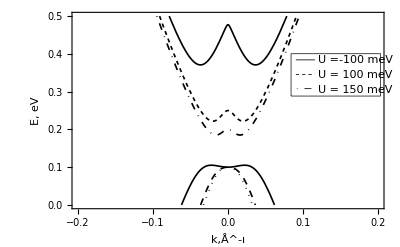

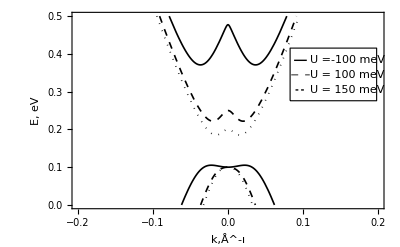

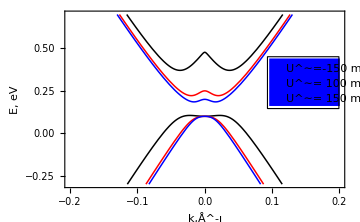

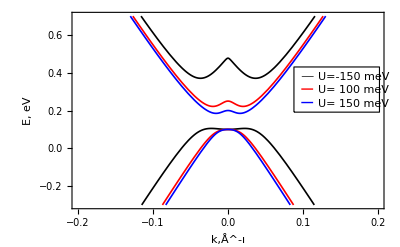

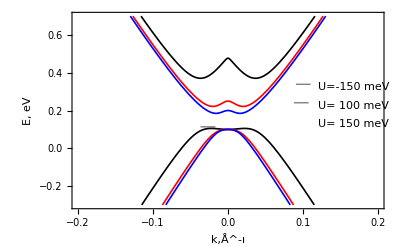

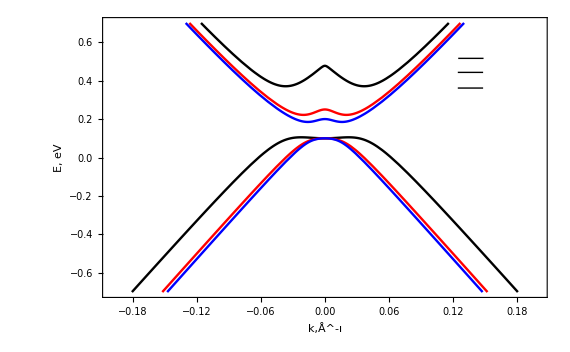

```mathematica
Export["99992.pdf",Plot[{f1[x,-0.1],f4[x,-0.1],f1[x,0.1],f4[x,0.1],f1[x,0.15],f4[x,0.15]},{x,-0.1,0.1},AxesLabel->{"k,A^-1",EeV},PlotRange->{-0.3,0.7},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Blue}},Frame->True]]
```

99992.pdf

```mathematica
d1:=0.15
data1=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]]+0.07,x][[1]]},{α,-0.25,0.45,0.05}];
d1:=-0.05 
data2=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]+0.02],x][[1]]},{α,-0.25,0.45,0.05}];
```

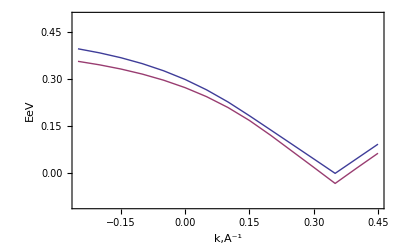

```mathematica
ListPlot[{data1,data2},Joined->True,PlotRange->{-0.1,0.5},AxesLabel->{"k,A^-1",EeV},Frame->True]
```